```mathematica
ClearAll["Global`*"]
```

```mathematica
(*定义常微分方程组*)
eqns={
-c U-q U^3+(3/2) q U V-(q/4) U'',
-c V+(3/4) q V^2-3 q U^2 V+(3 q/4) (U')^2+(3 q/2) U U''-(1/4) q V''
};
```

```mathematica
(*定义新的函数形式和导数法则*)
S[Y_]:=Subscript[a, 0]+Subscript[a, 1] Y
P[Y_]:=Subscript[b, 0]+Subscript[b, 1] Y+Subscript[b, 2] Y^2
DU=(1-Y^2) S'[Y];
D2U=(1-Y^2) (-2 Y S'[Y]+(1-Y^2) S''[Y]);
DV=(1-Y^2) P'[Y];
D2V=(1-Y^2) (-2 Y P'[Y]+(1-Y^2) P''[Y]);
```

```mathematica
(*替换 U 的导数和二阶导数*)
eqnsSub=eqns/. {U->S[Y],V->P[Y],U'->DU,U''->D2U,V'->DV,V''->D2V}
eqnsSub//Column
```

{1/2 q Y (1-Y^2) a_1-c (a_0+Y a_1)-q (a_0+Y a_1)^3+3/2 q (a_0+Y a_1) (b_0+Y b_1+Y^2 b_2),3/4 q (1-Y^2)^2 a_1^2-3 q Y (1-Y^2) a_1 (a_0+Y a_1)-c (b_0+Y b_1+Y^2 b_2)-3 q (a_0+Y a_1)^2 (b_0+Y b_1+Y^2 b_2)+3/4 q (b_0+Y b_1+Y^2 b_2)^2-1/4 q (1-Y^2) (2 (1-Y^2) b_2-2 Y (b_1+2 Y b_2))}

1/2 q Y (1-Y^2) a_1-c (a_0+Y a_1)-q (a_0+Y a_1)^3+3/2 q (a_0+Y a_1) (b_0+Y b_1+Y^2 b_2)
3/4 q (1-Y^2)^2 a_1^2-3 q Y (1-Y^2) a_1 (a_0+Y a_1)-c (b_0+Y b_1+Y^2 b_2)-3 q (a_0+Y a_1)^2 (b_0+Y b_1+Y^2 b_2)+3/4 q (b_0+Y b_1+Y^2 b_2)^2-1/4 q (1-Y^2) (2 (1-Y^2) b_2-2 Y (b_1+2 Y b_2))

```mathematica
(*展开得到关于 Y 的表达式*)
expandedEqns=Expand[eqnsSub];
# ==0&/@expandedEqns //Column
```

-c a_0-q a_0^3-c Y a_1+1/2 q Y a_1-1/2 q Y^3 a_1-3 q Y a_0^2 a_1-3 q Y^2 a_0 a_1^2-q Y^3 a_1^3+3/2 q a_0 b_0+3/2 q Y a_1 b_0+3/2 q Y a_0 b_1+3/2 q Y^2 a_1 b_1+3/2 q Y^2 a_0 b_2+3/2 q Y^3 a_1 b_2==0
-3 q Y a_0 a_1+3 q Y^3 a_0 a_1+(3 q a_1^2)/4-9/2 q Y^2 a_1^2+15/4 q Y^4 a_1^2-c b_0-3 q a_0^2 b_0-6 q Y a_0 a_1 b_0-3 q Y^2 a_1^2 b_0+(3 q b_0^2)/4-c Y b_1+1/2 q Y b_1-1/2 q Y^3 b_1-3 q Y a_0^2 b_1-6 q Y^2 a_0 a_1 b_1-3 q Y^3 a_1^2 b_1+3/2 q Y b_0 b_1+3/4 q Y^2 b_1^2-(q b_2)/2-c Y^2 b_2+2 q Y^2 b_2-3/2 q Y^4 b_2-3 q Y^2 a_0^2 b_2-6 q Y^3 a_0 a_1 b_2-3 q Y^4 a_1^2 b_2+3/2 q Y^2 b_0 b_2+3/2 q Y^3 b_1 b_2+3/4 q Y^4 b_2^2==0

```mathematica
(*令 Y 的各个次幂系数为零*)
coeffEqns=Flatten[CoefficientList[expandedEqns,Y]];
eqnShow = # ==0&/@coeffEqns ;
allY=Join[Table[Inactivate[Y^n,Power],{n,0,3}],Table[Inactivate[Y^n,Power],{n,0,4}]];
Grid[Transpose[{allY,eqnShow }]]
```

Y^0 | -c a_0-q a_0^3+3/2 q a_0 b_0==0
Y^1 | -c a_1+(q a_1)/2-3 q a_0^2 a_1+3/2 q a_1 b_0+3/2 q a_0 b_1==0
Y^2 | -3 q a_0 a_1^2+3/2 q a_1 b_1+3/2 q a_0 b_2==0
Y^3 | -(q a_1)/2-q a_1^3+3/2 q a_1 b_2==0
Y^0 | (3 q a_1^2)/4-c b_0-3 q a_0^2 b_0+(3 q b_0^2)/4-(q b_2)/2==0
Y^1 | -3 q a_0 a_1-6 q a_0 a_1 b_0-c b_1+(q b_1)/2-3 q a_0^2 b_1+3/2 q b_0 b_1==0
Y^2 | -9/2 q a_1^2-3 q a_1^2 b_0-6 q a_0 a_1 b_1+(3 q b_1^2)/4-c b_2+2 q b_2-3 q a_0^2 b_2+3/2 q b_0 b_2==0
Y^3 | 3 q a_0 a_1-(q b_1)/2-3 q a_1^2 b_1-6 q a_0 a_1 b_2+3/2 q b_1 b_2==0
Y^4 | (15 q a_1^2)/4-(3 q b_2)/2-3 q a_1^2 b_2+(3 q b_2^2)/4==0

```mathematica
(*得到代数决定方程组*)
```

```mathematica
eqnList=Thread[coeffEqns==0]
```

{-c a_0-q a_0^3+3/2 q a_0 b_0==0,-c a_1+(q a_1)/2-3 q a_0^2 a_1+3/2 q a_1 b_0+3/2 q a_0 b_1==0,-3 q a_0 a_1^2+3/2 q a_1 b_1+3/2 q a_0 b_2==0,-(q a_1)/2-q a_1^3+3/2 q a_1 b_2==0,(3 q a_1^2)/4-c b_0-3 q a_0^2 b_0+(3 q b_0^2)/4-(q b_2)/2==0,-3 q a_0 a_1-6 q a_0 a_1 b_0-c b_1+(q b_1)/2-3 q a_0^2 b_1+3/2 q b_0 b_1==0,-9/2 q a_1^2-3 q a_1^2 b_0-6 q a_0 a_1 b_1+(3 q b_1^2)/4-c b_2+2 q b_2-3 q a_0^2 b_2+3/2 q b_0 b_2==0,3 q a_0 a_1-(q b_1)/2-3 q a_1^2 b_1-6 q a_0 a_1 b_2+3/2 q b_1 b_2==0,(15 q a_1^2)/4-(3 q b_2)/2-3 q a_1^2 b_2+(3 q b_2^2)/4==0}

```mathematica
(*解代数决定方程组，得到关于 c,a0,a1,b0,b1,b2 的表达式*)
(*添加附加约束条件*)
addConstraints={q!=0,Subscript[a, 1]!=0};
solutions=Solve[Join[eqnList,addConstraints],{Subscript[a, 0],Subscript[a, 1],Subscript[b, 0],Subscript[b, 1],Subscript[b, 2],q,c}];

solutions//Column
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{a_0→0,a_1→-1,b_0→-1,b_1→0,b_2→1,c→-q}
{a_0→-1/2,a_1→-1/2,b_0→-1/2,b_1→0,b_2→1/2,c→-q}
{a_0→0,a_1→-1/2,b_0→-1/2,b_1→0,b_2→1/2,c→-q/4}
{a_0→1/2,a_1→-1/2,b_0→-1/2,b_1→0,b_2→1/2,c→-q}
{a_0→-1/2,a_1→1/2,b_0→-1/2,b_1→0,b_2→1/2,c→-q}
{a_0→0,a_1→1/2,b_0→-1/2,b_1→0,b_2→1/2,c→-q/4}
{a_0→1/2,a_1→1/2,b_0→-1/2,b_1→0,b_2→1/2,c→-q}
{a_0→0,a_1→1,b_0→-1,b_1→0,b_2→1,c→-q}

Represent Nicer

```mathematica
solNice = Flatten[GatherBy[solutions,Last[#][[-1]]&],1];
solNice//Column
```

{a_0→0,a_1→-1,b_0→-1,b_1→0,b_2→1,c→-q}
{a_0→-1/2,a_1→-1/2,b_0→-1/2,b_1→0,b_2→1/2,c→-q}
{a_0→1/2,a_1→-1/2,b_0→-1/2,b_1→0,b_2→1/2,c→-q}
{a_0→-1/2,a_1→1/2,b_0→-1/2,b_1→0,b_2→1/2,c→-q}
{a_0→1/2,a_1→1/2,b_0→-1/2,b_1→0,b_2→1/2,c→-q}
{a_0→0,a_1→1,b_0→-1,b_1→0,b_2→1,c→-q}
{a_0→0,a_1→-1/2,b_0→-1/2,b_1→0,b_2→1/2,c→-q/4}
{a_0→0,a_1→1/2,b_0→-1/2,b_1→0,b_2→1/2,c→-q/4}

```mathematica
vNicer=Subscript[b, 0]+Subscript[b, 1]*Tanh[x-c*t]+Subscript[b, 2]*Tanh[x-c*t]^2/.solNice;
uNicer =Subscript[a, 0]+Subscript[a, 1] Tanh[x-c*t]/.solNice;
Grid[Transpose[{c/.solNice,MapIndexed[Subscript[u, First[#2]]->#1&,uNicer],MapIndexed[Subscript[v, First[#2]]->#1&,vNicer]}]]
```

-q | u_1→-Tanh[q t+x] | v_1→-1+Tanh[q t+x]^2
-q | u_2→-1/2-1/2 Tanh[q t+x] | v_2→-1/2+1/2 Tanh[q t+x]^2
-q | u_3→1/2-1/2 Tanh[q t+x] | v_3→-1/2+1/2 Tanh[q t+x]^2
-q | u_4→-1/2+1/2 Tanh[q t+x] | v_4→-1/2+1/2 Tanh[q t+x]^2
-q | u_5→1/2+1/2 Tanh[q t+x] | v_5→-1/2+1/2 Tanh[q t+x]^2
-q | u_6→Tanh[q t+x] | v_6→-1+Tanh[q t+x]^2
-q/4 | u_7→-1/2 Tanh[(q t)/4+x] | v_7→-1/2+1/2 Tanh[(q t)/4+x]^2
-q/4 | u_8→1/2 Tanh[(q t)/4+x] | v_8→-1/2+1/2 Tanh[(q t)/4+x]^2

图像，参数为-》 2

```mathematica
para1=2;
setting1={ClippingStyle->None,
Exclusions->"Singularities",
PlotRange->Automatic,
ColorFunction-> "TemperatureMap",PlotPoints->60(* 60很顺滑*)

};
f[x_,t_]:=1/2-1/2 Tanh[q t+x];g[x_,t_]:=-1/2+1/2 Tanh[q t+x]^2;
GraphicsRow[
{
Plot3D[f[x,t]/.q->para1,{x,-10,10},{t,0,3},Evaluate[setting1],AxesLabel->{"x","t","U"," "},PlotLabel->Row[{"u_3=",f[x,t]}]],
Plot3D[g[x,t]/.q->para1,{x,-10,10},{t,0,3},Evaluate[setting1],AxesLabel->{"x","t","U"," "},PlotLabel->Row[{"v_3=",g[x,t]}]]
},ImageSize->800]
```

-Graphics-

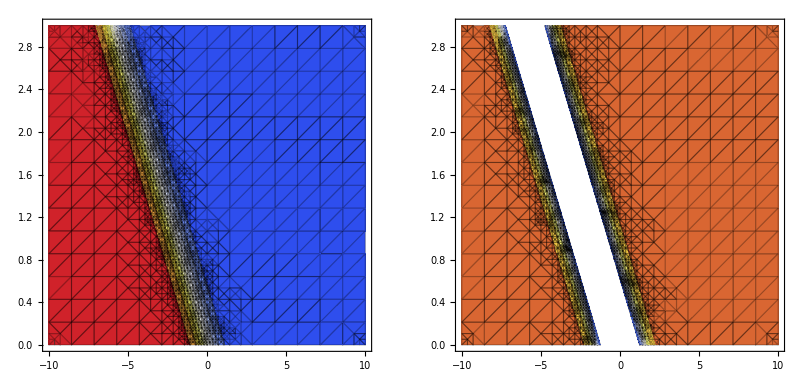

```mathematica
GraphicsRow[
{ContourPlot[f[x,t],{x,-10,10},{t,0,3},Mesh->All,ColorFunction->"TemperatureMap"],
ContourPlot[g[x,t],{x,-10,10},{t,0,3},Mesh->All,ColorFunction->"TemperatureMap"]},ImageSize->800]
```

```mathematica
MapIndexed[Subscript[u, First[#2]]->#1&,{a,b,c,d}]
MapIndexed[Subscript[u, First[#2+10]]->#1&,{a,b,c,d}]
```

{u_1→a,u_2→b,u_3→c,u_4→d}

{u_11→a,u_12→b,u_13→c,u_14→d}

验证放最后，因为不会run了

```mathematica
peqns={D[u[x,t],t]-3 q u[x,t]^2 D[u[x,t],x]+(3/2) q D[(u[x,t] v[x,t]),x]-(1/4) q D[u[x,t],{x,3}]==0,D[v[x,t],t]+(3/2) q v[x,t] D[v[x,t],x]-3 q D[(u[x,t]^2 v[x,t]),x]+3 q D[u[x,t],x] D[u[x,t],{x,2}]+(3/2) q u[x,t] D[u[x,t],{x,3}]-(1/4) q D[v[x,t],{x,3}]==0};

solV=v->Function[{x,t},Subscript[b, 0]+Subscript[b, 1]*Tanh[x-c*t]+Subscript[b, 2]*Tanh[x-c*t]^2]
solU=u->Function[{x,t},Subscript[a, 0]+Subscript[a, 1] Tanh[x-c*t]]

peqns/. {solV/. solutions[[1]],solU/. solutions[[1]]}//FullSimplify
```

v→Function[{x,t},b_0+b_1 Tanh[x-c t]+b_2 Tanh[x-c t]^2]

u→Function[{x,t},a_0+a_1 Tanh[x-c t]]

{True,True}

```mathematica
Map[(peqns/. {solV/. #,solU/. #}//FullSimplify)&,solutions]//Column
```

{True,True}
{True,True}
{True,True}
{True,True}
{True,True}
{True,True}
{True,True}
{True,True}